## Haploid recursion equation

```mathematica
Clear["Global`*"]
```

Equation 1.1 when incorporating both fecundity and mortality selection:

```mathematica
pt1=pt wA/(pt wA+(1-pt)wB)
```

(pt wA)/(pt wA+(1-pt) wB)

Difference equation (Together[] function forces all terms to have the same denominator)):

```mathematica
Δp=pt1-pt//Together//Simplify
```

-((-1+pt) pt (wA-wB))/(pt (wA-wB)+wB)

## McElreath & Boyd eq. 1.2

Using Mathematica’s Rsolve function, no trouble solving this explicitly.

```mathematica
recursol=RSolve[{p[t+1]==p[t]wA/(p[t]wA+(1-p[t])wB),p[0]==pinit},p[t],t]//Flatten//Simplify
```

{p[t]→pinit/(pinit+(wB/wA)^t-pinit (wB/wA)^t)}

## Reproducing Figure 1.2:

Plot the explicit solution:

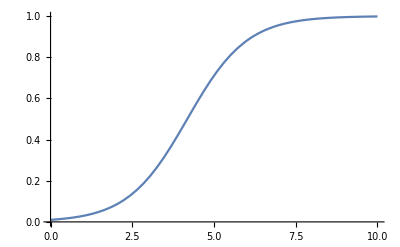

```mathematica
Plot[p[t]/.recursol/.{pinit->0.01,wB->0.5,wA->1.5},{t,0,10}]
```

## Cobweb plot code:

See also 	 for a good piece of cobweb plot. However, for the sake of documentation I have made my own plot here (let me know if it breaks down):

```mathematica
ClearAll[CobwebPlot]
Options[CobwebPlot]=Join[{CobStyle->Automatic},Options[Graphics]];
CobwebPlot[f_,start_?NumericQ,n_,xrange:{xmin_,xmax_},opts:OptionsPattern[]]:=Module[{cob,x,g1,coor},cob=NestList[f,N[start],n];
coor=Partition[Riffle[cob,cob],2,1];
coor[[1,2]]=0;
cobstyle=OptionValue[CobwebPlot,CobStyle];
cobstyle=If[cobstyle===Automatic,Red,cobstyle];
g1=Graphics[{cobstyle,Line[coor]}];
Show[{Plot[{x,f[x]},{x,xmin,xmax},PlotStyle->{{Thick,Black},Black}],g1},FilterRules[{opts},Options[Graphics]]]]
```

And here an example. Rather than writing p wA / (p wA + (1-p) wB) we write the p as a # and then close off the expression with an ampersand ‘&’ so that mathematica knows this is our variable, rather than a parameter. 

We start from starting value 0.1, go for 10 iterations and the range of the x-axis is from 0 to 1. There are also some additional styling options you can explore for yourself

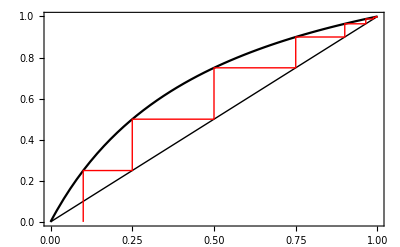

```mathematica
CobwebPlot[# wA/(# wA+(1-#)wB)&/.{wA->1.5,wB->0.5},0.1,10,{0,1},PlotRange->{Automatic,{0,1}},Frame->True,Axes->False,CobStyle->Red,PlotRangePadding->None]
```

## Equilibria

Solve for the equilibira of the haploid model:

```mathematica
Solve[Δp==0,pt]//Flatten
```

{pt→0,pt→1}

## Stability analysis

First calculate the derivative dp(t+1) / dp(t) using the D operator, then substitute for the respective equilibria

```mathematica
dpt1dp=D[pt1,pt]
```

-(pt wA (wA-wB))/(pt wA+(1-pt) wB)^2+wA/(pt wA+(1-pt) wB)

```mathematica
stabcond0=dpt1dp/.pt->0
```

wA/wB

The equilibrium p = 0 is stable when dp(t+1) / dp(t)|p=0 < 1, or when wA < wB

```mathematica
stabcond1=dpt1dp/.pt->1//Simplify
```

wB/wA

The equilibrium p = 1 is stable when dp(t+1) / dp(t)|p=1 < 1, or when wA > wB